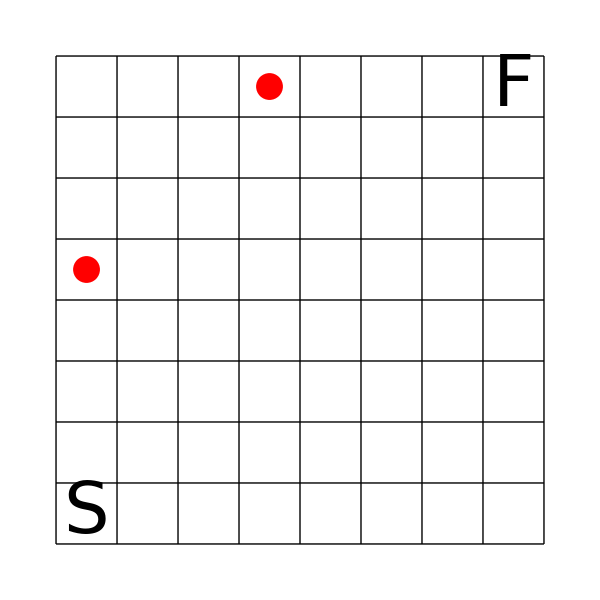
-Graphics- -Graphics-

```mathematica
dir={{1,0},{-1,0},{0,1},{0,-1}};
```

```mathematica
pick[a_,b_]:=Select[solns,Intersection[#[[2]],b]=={}&& Complement[a,#[[1]]]=={}&]
```

```mathematica
pic[L_]:=Style[Graphics[{
Table[Line[{{0,i},{n,i}}],{i,0,n}],Table[Line[{{i,0},{i,n}}],{i,0,n}],
AbsoluteThickness[2],Orange,Line[Map[#-{1/2,1/2}&,L[[1]]]],
Red,Map[Disk[#-{1/2,1/2},.22]&,L[[1]]]},ImageSize->14n,PlotRange->{{-.02,n+.02},{-.02,n+.02}}],Antialiasing->False]
```

```mathematica
beforepic[L_,M_]:=Style[Graphics[{
Table[Line[{{0,i},{n,i}}],{i,0,n}],Table[Line[{{i,0},{i,n}}],{i,0,n}],
Text[Style["S",FontSize->12],{1/2,1/2}],Text[Style["F",FontSize->12],{n-1/2,n-1/2}],
Map[Rectangle[#,#-1]&,M],AbsoluteThickness[2],
Red,Map[Disk[#-{1/2,1/2},.22]&,L]},ImageSize->14n,PlotRange->{{-.02,n+.02},{-.02,n+.02}}],Antialiasing->False]
```

```mathematica
n=8;jump=3;
stack={{{{1,1}},{{1,1}},1}};
solns={};
While[Length[stack]>0,
top=First[stack];
stack=Rest[stack];
nodes=top[[1]];
path=top[[2]];
nextnum=top[[3]];
If[Last[nodes]=={n,n},AppendTo[solns,top]];
next=Select[Map[Last[nodes]+#&,nextnum*dir],1≤#[[1]]≤n&&1≤#[[2]]≤n&&Not[MemberQ[path,#]]&];
next=Select[next,Intersection[path,Table[i Last[nodes]+(1-i)#,{i,0,1-1/nextnum,1/nextnum}]]=={}&];
For[j=1,j≤Length[next],j++,
PrependTo[stack,{Join[nodes,{next[[j]]}],Join[path,Table[i Last[nodes]+(1-i)next[[j]],{i,0,1-1/nextnum,1/nextnum}]],Mod[nextnum,jump]+1}]]
];
Print[Length[solns]]
```

340

```mathematica
MatrixForm[Table[Length[Select[solns,MemberQ[#[[1]],{i,j}]&]],{i,1,n},{j,1,n}]]
```

(62 | 40 | 0 | 37 | 0 | 0 | 27
40 | 22 | 13 | 1 | 18 | 13 | 40
0 | 13 | 0 | 9 | 6 | 2 | 1
37 | 1 | 9 | 36 | 21 | 0 | 40
0 | 18 | 6 | 21 | 10 | 8 | 2
0 | 13 | 2 | 0 | 8 | 0 | 2
27 | 40 | 1 | 40 | 2 | 2 | 62)

```mathematica
Map[pic,solns]
```

## 2

```mathematica
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
For[k=i,k≤n,k++,
For[l=1,l≤n,l++,
a=pick[{},{{i,j},{k,l}}];
If[Length[a]==1,Print[beforepic[{},{{i,j},{k,l}}]," ",pic[a[[1]]]]]]]]]
```

```mathematica
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
For[k=1,k≤n,k++,
For[l=1,l≤n,l++,
a=pick[{{i,j}},{{k,l}}];
If[Length[a]==1,Print[beforepic[{{i,j}},{{k,l}}]," ",pic[a[[1]]]]]]]]]
```

$Aborted

```mathematica
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
For[k=i,k≤n,k++,
For[l=1,l≤n,l++,
a=pick[{{i,j},{k,l}},{}];
If[Length[a]==1,Print[beforepic[{{i,j},{k,l}},{}]," ",pic[a[[1]]]]]]]]]
```

-Graphics- -Graphics-

-Graphics- -Graphics-

-Graphics- -Graphics-

«138 more identical outputs»

## 3

```mathematica
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
For[k=i,k≤n,k++,
For[l=1,l≤n,l++,
For[m=k,m≤n,m++,
For[mm=1,mm≤n,mm++,
a=pick[{},{{i,j},{k,l},{m,mm}}];
If[Length[a]==1,Print[beforepic[{},{{i,j},{k,l},{m,mm}}]," ",pic[a[[1]]]]]]]]]]]
```

$Aborted

```mathematica
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
For[k=i,k≤n,k++,
For[l=1,l≤n,l++,
For[m=k,m≤n,m++,
For[mm=1,mm≤n,mm++,
For[p=m,p≤n,p++,
For[pp=1,pp≤n,pp++,
a=pick[{},{{i,j},{k,l},{m,mm},{p,pp}}];
If[Length[a]==1,Print[beforepic[{},{{i,j},{k,l},{m,mm},{p,pp}}]," ",pic[a[[1]]]]]]]]]]]]]
```

```mathematica
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
For[k=1,k≤n,k++,
For[l=1,l≤n,l++,
For[m=k,m≤n,m++,
For[mm=1,mm≤n,mm++,
a=pick[{{i,j}},{{k,l},{m,mm}}];
If[Length[a]==1,Print[beforepic[{{i,j}},{{k,l},{m,mm}}]," ",pic[a[[1]]]]]]]]]]]
```

```mathematica
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
For[k=i,k≤n,k++,
For[l=1,l≤n,l++,
For[m=1,m≤n,m++,
For[mm=1,mm≤n,mm++,
a=pick[{{i,j},{k,l}},{{m,mm}}];
If[Length[a]==1,Print[beforepic[{{i,j},{k,l}},{{m,mm}}]," ",pic[a[[1]]]]]]]]]]]
```

```mathematica
For[i=1,i≤n,i++,
For[j=1,j≤n,j++,
For[k=i,k≤n,k++,
For[l=1,l≤n,l++,
For[m=k,m≤n,m++,
For[mm=1,mm≤n,mm++,
a=pick[{{i,j},{k,l},{m,mm}},{}];
If[Length[a]==1,Print[beforepic[{{i,j},{k,l},{m,mm}},{}]," ",pic[a[[1]]]]]]]]]]]
```